```mathematica
P0[x_]=2(x-1/2)(x-1);
P1[x_]=4x(1-x);
P2[x_]=(2x-1)x;
```

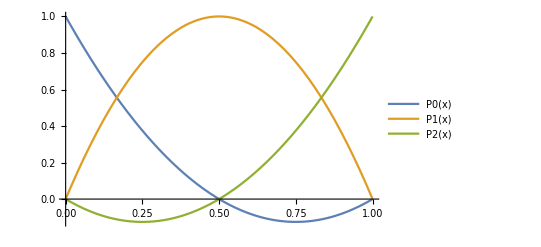

```mathematica
Plot[{P0[x], P1[x],P2[x]},{x, 0,1},PlotLegends->"Expressions"]
```

```mathematica
A[f_,g_]=Integrate[D[f[x],x]*D[g[x],x],{x, 0, 1}];
{{A[P0, P0],A[P0,P1], A[P0,P2]},
{A[P1, P0],A[P1,P1], A[P1,P2]},
{A[P2, P0],A[P2,P1], A[P2,P2]}}//MatrixForm
```

(7/3 | -8/3 | 1/3
-8/3 | 16/3 | -8/3
1/3 | -8/3 | 7/3)

```mathematica
{Integrate[P0[x],{x, 0,1}],Integrate[P1[x],{x, 0,1}],Integrate[P2[x],{x, 0,1}]}
```

{1/6,2/3,1/6}

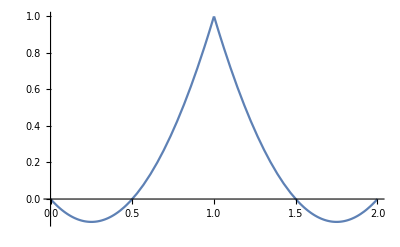

```mathematica
Plot[Piecewise[{{P2[x],0<x<1},{P0[x-1], 1<=x<2}}],{x, 0,2}]
```

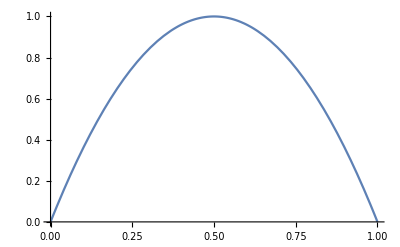

```mathematica
Plot[P1[x],{x, 0,1}]
```